4 LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]-s y[0]-y'[0]==(1+s)/(4+(1+s)^2)

1+4 LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]==(1+s)/(4+(1+s)^2)

{{LaplaceTransform[y[t],t,s]→(-4-s-s^2)/((4+s^2) (5+2 s+s^2))}}

(1/34-(2 ⅈ)/17) ⅇ^((-1-2 ⅈ) t)+(1/34+(2 ⅈ)/17) ⅇ^((-1+2 ⅈ) t)-1/17 Cos[2 t]-4/17 Sin[2 t]

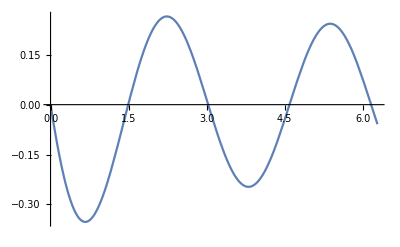

```mathematica
paso1=LaplaceTransform[y''[t]+ 4y[t] == Exp[-t]Cos[2t],t,s]
paso2=paso1/.{y[0]->0, y'[0]->-1}
paso3 = Solve[paso2,LaplaceTransform[y[t],t,s]]
sol=Simplify[InverseLaplaceTransform[(-4-s-s^2)/((4+s^2) (5+2 s+s^2)),s,t]]//Expand
Plot[sol,{t, 0, 2Pi}]
```